TRAPEZOIDAL RULE

```mathematica
Plot[-x^2+2,{x,0,1},GridLines->{{0.1,0.2,0.3,0.4,0.5},{0}},PlotLabel->{"f(x)","h=(b - a)/n"}]
```

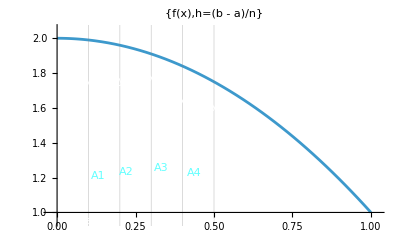

A_1=h((y_0+y_1)/2)

A_T=A_1+A_2+A_3+A_4

A_2=h((y_1+y_2)/2),  A_3=h((y_2+y_3)/2), and A_4=h((y_3+y_4)/2). The total area now is
A_T=h/2(y_0+2 y_1+2 y_2+2 y_3+y_4)

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

===================================================================================

SIMULATION BY MATHEMATICA

```mathematica
(*Define the function*)f[x_]:=x^2

(*Integration limits*)
a=0;
b=2;
n=10;

(*Step size*)
h=(b-a)/n;

(*Generate the x-values*)
xValues=Table[a+i*h,{i,0,n}];

(*Evaluate f(x) at each point*)
fValues=f/@xValues;

(*Apply Trapezoidal Rule formula*)
approxIntegral=(h/2)*(fValues[[1]]+2*Sum[fValues[[i]],{i,2,n}]+fValues[[n+1]])

(*Optional:Compare with exact value*)
exactIntegral=Integrate[x^2,{x,0,2}]
error=approxIntegral-exactIntegral
```

67/25

8/3

1/75

```mathematica
67.0/25
```

2.68

-Graphics-

-Graphics-

=============================================================================